## Cálculo de las secciones transversales empleando el modelo Drude-Lorentz y corrección de tamaño

En este Notebook se emplean las definiciones del modelo de Drude-Lorentz de Rakic en https://doi.org/10.1364/ao.37.005271
- Para el modelo de Drude se emplea
ϵ_Drude=1-(f_0 ω_p^2)/(ω (ω - i γ_0))
- Para el modelo de Lorentz se emplea
ϵ_Lorentz=∑_(j=1)^k 1+(f_j ω_p^2)/(ω_j^2-ω^2-iγω)
de tal forma que se obtiene

```mathematica
h=4.135667696*10^(-15); (*eV s*)
hbar=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
hvFAu=(1.40*10^(15))*hbar;(*nm/s*)
hvFAg=1.39*10^(15)*hbar;(*nm/s*)
```

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+((1/(2*Sqrt[eab2]))* Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]));
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
polarizability[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_]:=Module[{ϵDrude,ϵOC,ϵTot,ϵm,k,αx,αz,αxDrude,αzDrude,αxOC,αzOC},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
								ϵDrude=1-((f[[1]]*wp^2)/((w)(w+I * g[[1]])));
								ϵOC=Sum[oroscoCoimbraModel[w0[[i]],sigma[[i]],w,g[[i]],mu,wp,f[[i]]],{i,2,Length[w0]}];
										ϵTot=ϵDrude+ϵOC;
										αx=4 π a b c  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b c ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxDrude=4 π a b c ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵDrude-ϵm)));
										αzDrude=4 π a b c ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵDrude-ϵm)));
										αxOC=4 π a b c  ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵOC-ϵm)));
										αzOC=4 π a b c ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵOC-ϵm)));
										{αx,αz,αxDrude,αzDrude,αxOC,αzOC}]
```

```mathematica
Cabs[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_]:=Module[{ϵDrude,ϵOC,ϵTot,ϵm,k,αx,αz,αxDrude,αzDrude,αxOC,αzOC,CabsDrude,CabsOC,Cabs},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
ϵDrude=1-((f[[1]]*wp^2)/((w)(w+I * g[[1]])));
								ϵOC=Sum[oroscoCoimbraModel[w0[[i]],sigma[[i]],w,g[[i]],mu,wp,f[[i]]],{i,2,Length[w0]}];
										ϵTot=ϵDrude+ϵOC;
										αx=4 π a b c  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b c ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxDrude=4 π a b c  ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵDrude-ϵm)));
										αzDrude=4 π a b c ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵDrude-ϵm)));
										αxOC=4 π a b c  ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵOC-ϵm)));
										αzOC=4 π a b c((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵOC-ϵm)));
										Cabs=k Im[2 αx+αz]/3;
										CabsDrude=k Im[2 αxDrude+αzDrude]/3;
										CabsOC=k Im[2 αxOC+αzOC]/3;{Cabs,CabsDrude,CabsOC}]
```

```mathematica
Csca[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_]:=Module[{ϵDrude,ϵOC,ϵTot,ϵm,k,αx,αz,αxDrude,αzDrude,αxOC,αzOC,CscaDrude,CscaOC,Csca},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
ϵDrude=1-((f[[1]]*wp^2)/((w)(w+I * g[[1]])));
								ϵOC=Sum[oroscoCoimbraModel[w0[[i]],sigma[[i]],w,g[[i]],mu,wp,f[[i]]],{i,2,Length[w0]}];
										ϵTot=ϵDrude+ϵOC;
										αx=4 π a b c  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b c ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxDrude=4 π a b c  ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵDrude-ϵm)));
										αzDrude=4 π a b c ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵDrude-ϵm)));
										αxOC=4 π a b c2  ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵOC-ϵm)));
										αzOC=4 π a b c ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵOC-ϵm)));
										Csca=k^4 Norm[2 αx+αz]^2/(18 Pi);
										CscaDrude=k^4 Norm[2 αxDrude+αzDrude]^2/(18 Pi);
										CscaOC=k^4 Norm[2 αxOC+αzOC]^2/(18 Pi);{Csca,CscaDrude,CscaOC}]
```

```mathematica
Cext[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_]:=Csca[a,b,c,nm,w,wp,g,f,w0,sigma,mu]+Cabs[a,b,c,nm,w,wp,g,f,w0,sigma,mu];
```

```mathematica
qextAu0=Table[{w,Cext[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu][[1]]},{w,1,7,0.01}];
qextAu1=Table[{w,Cext[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu][[2]]},{w,1,7,0.01}];
qextAu3=Table[{w,Cext[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu][[3]]},{w,1,7,0.01}];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
h vlight/2.44
```

508.484

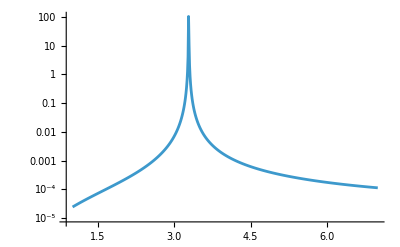

```mathematica
ListLinePlot[qextAu1,PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
qextAu3
```

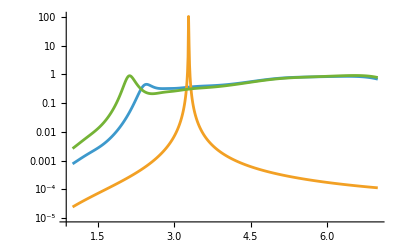

```mathematica
ListLinePlot[{qextAu0,qextAu1,qextAu3},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
eps[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_,hvF_]:=Module[{ϵDrude,gammaSC,ϵOC,ϵTot,ϵm,k,αx,αz,αxDrude,αzDrude,αxOC,αzOC},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
										gammaSC=g[[1]]+(hvF/(a b c)^(1/3));
										ϵDrude=1-((f[[1]]*wp^2)/((w)(w+I * gammaSC)));
								ϵOC=1+Sum[oroscoCoimbraModel[w0[[i]],sigma[[i]],w,g[[i]],mu,wp,f[[i]]],{i,2,Length[w0]}];
										ϵTot=ϵDrude+ϵOC-1;
										{ϵTot,ϵDrude,ϵOC}]
polarizabilitySC[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_,hvF_]:=Module[{ϵDrude,gammaSC,ϵOC,ϵTot,ϵm,k,αx,αz,αxDrude,αzDrude,αxOC,αzOC},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
										gammaSC=g[[1]]+(hvF/(a b c)^(1/3));
										ϵDrude=1-((f[[1]]*wp^2)/((w)(w+I * gammaSC)));
								ϵOC=1+Sum[oroscoCoimbraModel[w0[[i]],sigma[[i]],w,g[[i]],mu,wp,f[[i]]],{i,2,Length[w0]}];
										ϵTot=ϵDrude+ϵOC-1;
										αx=4 π a b c  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b c ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxDrude=4 π a b c ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵDrude-ϵm)));
										αzDrude=4 π a b c ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵDrude-ϵm)));
										αxOC=4 π a b c  ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵOC-ϵm)));
										αzOC=4 π a b c ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵOC-ϵm)));
										{αx,αz,αxDrude,αzDrude,αxOC,αzOC}]
```

```mathematica
CabsSC[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_,hvF_]:=Module[{ϵDrude,gammaSC,ϵOC,ϵTot,ϵm,k,αx,αz,αxDrude,αzDrude,αxOC,αzOC,CabsDrude,CabsOC,Cabs},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
										gammaSC=g[[1]]+(hvF/(a b c)^(1/3));
										ϵDrude=1-((f[[1]]*wp^2)/((w)(w+I * gammaSC)));
								ϵOC=1+Sum[oroscoCoimbraModel[w0[[i]],sigma[[i]],w,g[[i]],mu,wp,f[[i]]],{i,2,Length[w0]}];
										ϵTot=ϵDrude+ϵOC-1;
										αx=4 π a b c ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b c ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxDrude=4 π a b c  ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵDrude-ϵm)));
										αzDrude=4 π a b c ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵDrude-ϵm)));
										αxOC=4 π a b c  ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵOC-ϵm)));
										αzOC=4 π a b c ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵOC-ϵm)));
										Cabs=k Im[2 αx+αz]/3;
										CabsDrude=k Im[2 αxDrude+αzDrude]/3;
										CabsOC=k Im[2 αxOC+αzOC]/3;{Cabs,CabsDrude,CabsOC}]
```

```mathematica
CscaSC[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_,hvF_]:=Module[{ϵDrude,gammaSC,ϵOC,ϵTot,ϵm,k,αx,αz,αxDrude,αzDrude,αxOC,αzOC,CscaDrude,CscaOC,Csca},
										ϵm=nm^2;
										k=(2 Pi nm w/(h vlight));
										gammaSC=g[[1]]+(hvF/(a b c)^(1/3));
										ϵDrude=1-((f[[1]]*wp^2)/((w)(w+I * gammaSC)));
								ϵOC=1+Sum[oroscoCoimbraModel[w0[[i]],sigma[[i]],w,g[[i]],mu,wp,f[[i]]],{i,2,Length[w0]}];
										ϵTot=ϵDrude+ϵOC-1;
										αx=4 π a b c ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b c ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										αxDrude=4 π a b c  ((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵDrude-ϵm)));
										αzDrude=4 π a b c((ϵDrude-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵDrude-ϵm)));
										αxOC=4 π a b c  ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵOC-ϵm)));
										αzOC=4 π a b c ((ϵOC-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵOC-ϵm)));
										Csca=k^4 Abs[2 αx+αz]^2/(18 Pi);
										CscaDrude=k^4 Abs[2 αxDrude+αzDrude]^2/(18 Pi);
										CscaOC=k^4 Abs[2 αxOC+αzOC]^2/(18 Pi);{Csca,CscaDrude,CscaOC}]
CextSC[a_,b_,c_,nm_,w_,wp_,g_,f_,w0_,sigma_,mu_,hvF_]:=CscaSC[a,b,c,nm,w,wp,g,f,w0,sigma,mu,hvF]+CabsSC[a,b,c,nm,w,wp,g,f,w0,sigma,mu,hvF];
```

### Oro

```mathematica
epsAuTotRe=Table[{w,Re[eps[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]]]},{w,1,7,0.01}];
epsAuDrudeRe=Table[{w,Re[eps[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[2]]]},{w,1,7,0.01}];
epsAuOCRe=Table[{w,Re[eps[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]]]},{w,1,7,0.01}];
epsAuTotIm=Table[{w,Im[eps[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]]]},{w,1,7,0.01}];
epsAuDrudeIm=Table[{w,Im[eps[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[2]]]},{w,1,7,0.01}];
epsAuOCIm=Table[{w,Im[eps[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]]]},{w,1,7,0.01}];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
qextAu0SC=Table[{w,CextSC[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]]},{w,1,15,0.01}];
qextAu1SC=Table[{w,CextSC[1.5,1.5,2.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]]},{w,1,15,0.01}];
qextAu3SC=Table[{w,CextSC[1.5,1.5,3.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]]},{w,1,15,0.01}];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
qextAu4SC=Table[{w,CextSC[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]]},{w,1,15,0.01}];
qextAu5SC=Table[{w,CextSC[1.5,1.5,2.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]]},{w,1,15,0.01}];
qextAu36SC=Table[{w,CextSC[1.5,1.5,3.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]]},{w,1,15,0.01}];
```

```mathematica
qextAu7SC=Table[{w,CextSC[1.5,1.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[2]]},{w,1,15,0.01}];
qextAu8SC=Table[{w,CextSC[1.5,1.5,2.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[2]]},{w,1,15,0.01}];
qextAu9SC=Table[{w,CextSC[1.5,1.5,3.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[2]]},{w,1,15,0.01}];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
h vlight/12
```

103.392

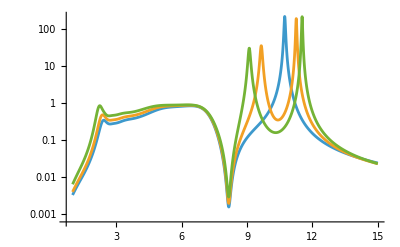

```mathematica
ListLinePlot[{qextAu0SC,qextAu1SC,qextAu3SC},PlotRange->All,ScalingFunctions->"Log"]
```

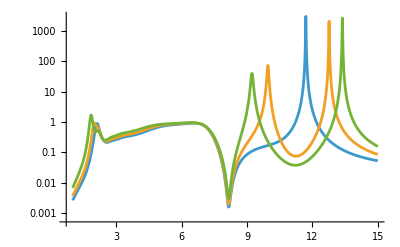

```mathematica
ListLinePlot[{qextAu4SC,qextAu5SC,qextAu36SC},PlotRange->All,ScalingFunctions->"Log"]
```

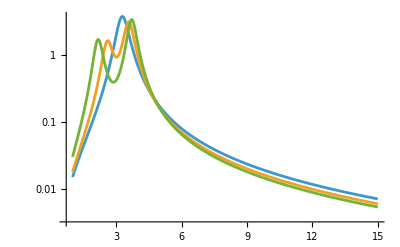

```mathematica
ListLinePlot[{qextAu7SC,qextAu8SC,qextAu9SC},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
barrido=Range[1.5,9.5,0.5];
barridosin1=Range[2,9.5,0.5];
omegasAu=Range[1,7,0.01];
AR=Range[1,9.5/1.5,1/3]
```

{1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3}

```mathematica
N[4/3]
2/1.5
9.5/1.5
```

1.33333

1.33333

6.33333

```mathematica
Length[barridosin1]
```

16

```mathematica
qextAuSCTotList=Table[{w,CextSC[#,#,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]]},{w,1,7,0.01}]&/@barrido;
qextAuSCTotBarrido=Table[CextSC[#,#,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]],{w,1,7,0.01}]&/@barrido;
qextAuSCTotPlot=Interpolation[Transpose[{omegasAu,qextAuSCTotBarrido[[#]]}]]&/@Range[1,17];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

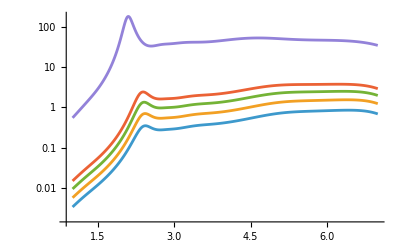

```mathematica
ListLinePlot[{qextAuSCTotList[[1]],qextAuSCTotList[[2]],qextAuSCTotList[[3]],qextAuSCTotList[[4]],qextAuSCTotList[[17]]},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
ListLinePlot[{qextAuSCTotList[[1]],qextAuSCTotList[[2]],qextAuSCTotList[[3]],qextAuSCTotList[[4]],qextAuSCTotList[[17]]},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics-

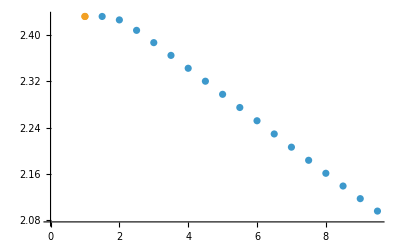

```mathematica
ResRojoAuTot=GoldenSearchMax[qextAuSCTotPlot[[#]],1.6,3] &/@Range[1,17];
ResSphereTot=GoldenSearchMax[qextAuSCTotPlot[[1]],2,3] ;
ListPlot[{Transpose[{barrido,ResRojoAuTot}],{{1,ResSphereTot}}}]
```

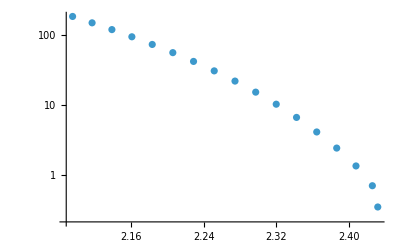

```mathematica
ListPlot[Table[{ResRojoAuTot[[x]],qextAuSCTotPlot[[x]][ResRojoAuTot[[x]]]},{x,1,17}],ScalingFunctions->"Log"]
```

```mathematica
qextAuSCDrudeList=Table[{w,CextSC[#,#,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[2]]},{w,1,7,0.01}]&/@barrido;
qextAuSCDrudeBarrido=Table[CextSC[#,#,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[2]],{w,1,7,0.01}]&/@barrido;
qextAuSCDrudePlot=Interpolation[Transpose[{omegasAu,qextAuSCDrudeBarrido[[#]]}]]&/@Range[1,17];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

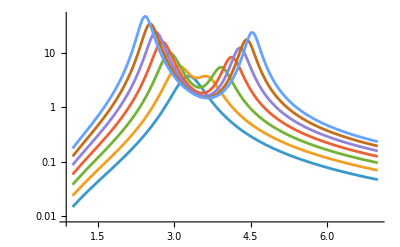

```mathematica
ListLinePlot[{qextAuSCDrudeList[[1]],qextAuSCDrudeList[[2]],qextAuSCDrudeList[[3]],qextAuSCDrudeList[[4]],qextAuSCDrudeList[[5]],qextAuSCDrudeList[[6]],qextAuSCDrudeList[[7]]},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
ResRojoAuDrude=GoldenSearchMax[qextAuSCDrudePlot[[#]],1.7,3.3] &/@Range[1,17]
ResAzulAuDrude=GoldenSearchMax[qextAuSCDrudePlot[[#]],3.2,6] &/@Range[1,17]
ResSphereDrude=GoldenSearchMax[qextAuSCDrudePlot[[1]],2,5] ;
```

{3.28242,3.08913,2.91146,2.76448,2.63744,2.52608,2.42753,2.33952,2.26021,2.18858,2.12311,2.06322,2.0082,1.95723,1.91,1.8659,1.82474}

{3.28242,3.61306,3.9171,4.12676,4.29038,4.42257,4.53172,4.62346,4.70161,4.76914,4.8279,4.8796,4.92532,4.96621,5.00283,5.03604,5.06611}

```mathematica
Length[ResAzulAuDrude]
Length[barridosin1]
```

16

16

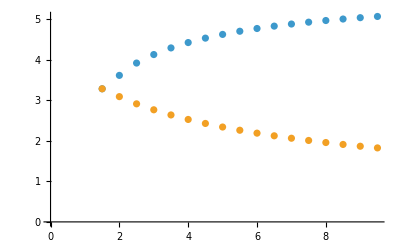

```mathematica
ListPlot[{Transpose[{barrido,ResAzulAuDrude}],Transpose[{barrido,ResRojoAuDrude}]}]
```

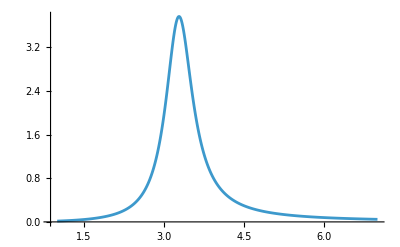

```mathematica
ListLinePlot[{qextAuSCDrudePlot[[1]]},PlotRange->All]
```

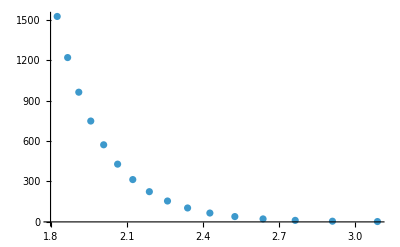

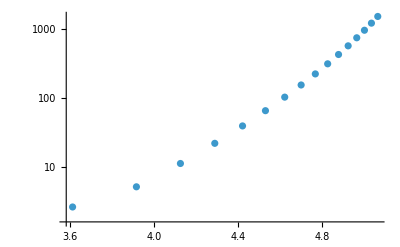

```mathematica
ListPlot[Table[{ResRojoAuDrude[[x]],qextAuSCDrudePlot[[x]][ResRojoAuDrude[[x]]]},{x,1,16}]]
ListPlot[Table[{ResAzulAuDrude[[x]],qextAuSCDrudePlot[[x]][ResRojoAuDrude[[x]]]},{x,1,16}],ScalingFunctions->"Log"]
```

```mathematica
qextAuSCOCList=Table[{w,CextSC[#,#,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]]},{w,1,7,0.01}]&/@barrido;
qextAuSCOCBarrido=Table[CextSC[#,#,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]],{w,1,7,0.01}]&/@barrido;
qextAuSCOCPlot=Interpolation[Transpose[{omegasAu,qextAuSCOCBarrido[[#]]}]]&/@Range[1,17];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

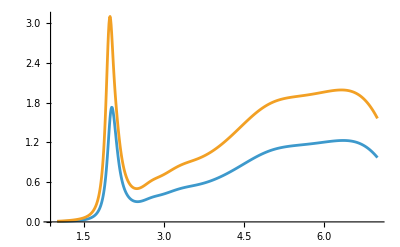

```mathematica
ListLinePlot[{qextAuSCOCList[[1]],qextAuSCOCList[[2]],qextAuSCOCList[[3]],qextAuSCOCList[[4]]},PlotRange->All]
```

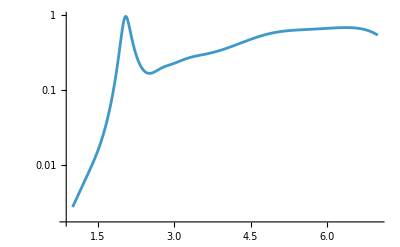

```mathematica
ListLinePlot[{qextAuSCOCList[[1]]},PlotRange->All,ScalingFunctions->"Log"]
```

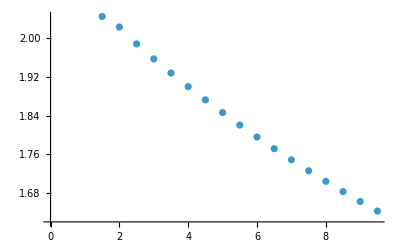

```mathematica
ResRojoAuOC=GoldenSearchMax[qextAuSCOCPlot[[#]],1.6,2.5] &/@Range[1,17];
ListPlot[Transpose[{barrido,ResRojoAuOC}]]
```

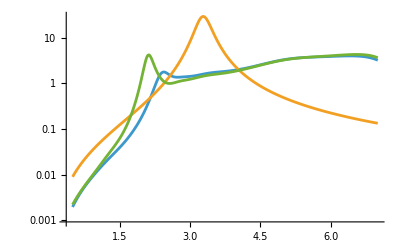

```mathematica
ListLinePlot[{qextAuSCTot,qextAuSCDrude,qextAuSCOC},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
1.5*5
```

7.5

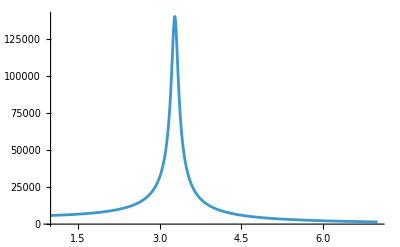

```mathematica
Plot[Interpolation[polAuSCDrudeListAbs1][x],{x,1,7},PlotRange->All]
```

```mathematica
polAuSCTotListAbs1=Table[{w,8*Abs[polarizabilitySC[7.5,7.5,7.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]]]/(4*Pi*7.5*7.5*7.5/3)},{w,1,7,0.01}];
polAuSCDrudeListAbs1=Table[{w,Abs[polarizabilitySC[7.5,7.5,7.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]]]/(4*Pi*7.5*7.5*7.5/3)},{w,1,7,0.01}];
polAuSCOCListAbs1=Table[{w,8*Abs[polarizabilitySC[7.5,7.5,7.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[5]]]/(4*Pi*7.5*7.5*7.5/3)},{w,1,7,0.01}];
polAuSCTotListArg1=Table[{w,Arg[polarizabilitySC[7.5,7.5,7.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[1]]]},{w,1,7,0.01}];
polAuSCDrudeListArg1=Table[{w,Arg[polarizabilitySC[7.5,7.5,7.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[3]]]},{w,1,7,0.01}];
polAuSCOCListArg1=Table[{w,Arg[polarizabilitySC[7.5,7.5,7.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[5]]]},{w,1,7,0.01}];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

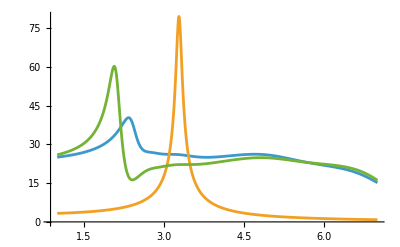

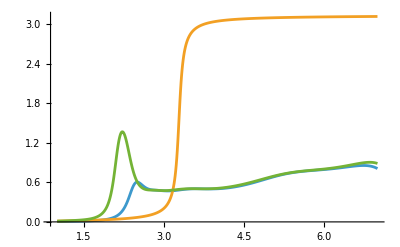

```mathematica
ListLinePlot[{polAuSCTotListAbs1,polAuSCDrudeListAbs1,polAuSCOCListAbs1},PlotRange->All]
ListLinePlot[{polAuSCTotListArg1,polAuSCDrudeListArg1,polAuSCOCListArg1},PlotRange->All]
```

```mathematica
polAuSCTotListAbs2=Table[{w,Abs[polarizabilitySC[7.5,7.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[#]]]/(4*Pi*7.5*7.5*1.5/3)},{w,1,7,0.01}]&/@{1,2};
polAuSCDrudeListAbs2=Table[{w,Abs[polarizabilitySC[7.5,7.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[#]]]/(4*Pi*7.5*7.5*1.5/3)},{w,1,7,0.01}]&/@{3,4};
polAuSCOCListAbs2=Table[{w,Abs[polarizabilitySC[7.5,7.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[#]]]/(4*Pi*7.5*7.5*1.5/3)},{w,1,7,0.01}]&/@{5,6};
polAuSCTotListArg2=Table[{w,Arg[polarizabilitySC[7.5,7.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[#]]]},{w,1,7,0.01}]&/@{1,2};
polAuSCDrudeListArg2=Table[{w,Arg[polarizabilitySC[7.5,7.5,1.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[#]]]},{w,1,7,0.01}]&/@{3,4};
polAuSCOCListArg2=Table[{w,Arg[polarizabilitySC[7.5,7.5,5.5,1,w,wpAu,gAu,fAu,w0Au,sigmaAu,mu,hvFAu][[#]]]},{w,1,7,0.01}]&/@{5,6};
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

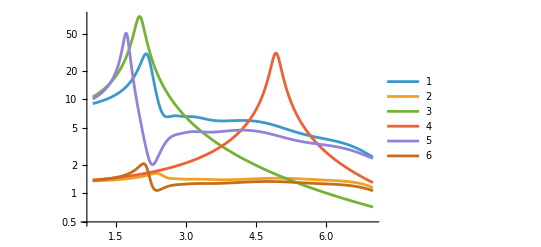

```mathematica
ListLinePlot[{polAuSCTotListAbs2[[1]],polAuSCTotListAbs2[[2]],polAuSCDrudeListAbs2[[1]],polAuSCDrudeListAbs2[[2]],polAuSCOCListAbs2[[1]],polAuSCOCListAbs2[[2]]},PlotRange->All,ScalingFunctions->"Log",PlotLegends->Automatic]
```

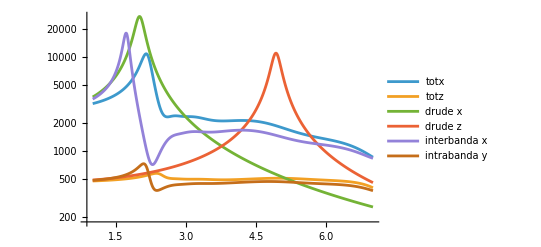

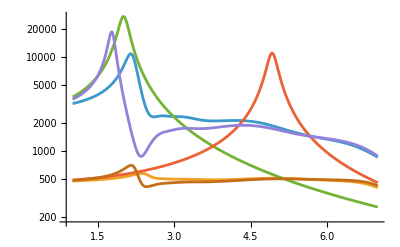

### Aluminio

```mathematica
barrido
```

{1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5}

```mathematica
omegasAl=Range[1,16,0.05];
```

```mathematica
epsAlTotRe=Table[{w,Re[eps[1.5,1.5,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[1]]]},{w,1,7,0.01}];
epsAlDrudeRe=Table[{w,Re[eps[1.5,1.5,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[2]]]},{w,1,7,0.01}];
epsAlOCRe=Table[{w,Re[eps[1.5,1.5,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[3]]]},{w,1,7,0.01}];
epsAlTotIm=Table[{w,Im[eps[1.5,1.5,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[1]]]},{w,1,7,0.01}];
epsAlDrudeIm=Table[{w,Im[eps[1.5,1.5,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[2]]]},{w,1,7,0.01}];
epsAlOCIm=Table[{w,Im[eps[1.5,1.5,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[3]]]},{w,1,7,0.01}];
```

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
qextAlSCTotList=Table[{w,CextSC[#,#,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[1]]},{w,1,16,0.05}]&/@barrido;
qextAlSCTotBarrido=Table[CextSC[#,#,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[1]],{w,1,16,0.05}]&/@barrido;
qextAlSCTotPlot=Interpolation[Transpose[{omegasAl,qextAlSCTotBarrido[[#]]}]]&/@Range[1,17];
```

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1474.97-314.994 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1474.97-314.994 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

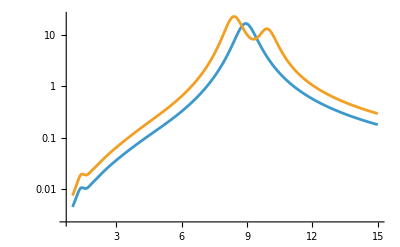

```mathematica
ListLinePlot[{qextAlSCTotList[[1]],qextAlSCTotList[[2]]},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
ResRojoAlTot=GoldenSearchMax[qextAlSCTotPlot[[#]],5,9.15] &/@Range[1,17]
ResAzulAlTot=GoldenSearchMax[qextAlSCTotPlot[[#]],9.4,15] &/@Range[2,17]
```

{8.94265,8.40755,7.94888,7.5567,7.21862,6.92226,6.65922,6.42534,6.21345,6.022,5.84779,5.68634,5.53762,5.39996,5.27023,5.15,5.03822}

{9.91176,10.6529,11.209,11.6488,12.0021,12.2976,12.5445,12.753,12.9366,13.0955,13.2344,13.3563,13.4673,13.5663,13.6553,13.7389}

```mathematica
qextAlSCDrudeList=Table[{w,CextSC[#,#,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[2]]},{w,1,16,0.05}]&/@barrido;
qextAlSCDrudeBarrido=Table[CextSC[#,#,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[2]],{w,1,16,0.05}]&/@barrido;
qextAlSCDrudePlot=Interpolation[Transpose[{omegasAl,qextAlSCDrudeBarrido[[#]]}]]&/@Range[1,17];
```

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1474.97-314.994 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1474.97-314.994 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
qextAlSCDrudePlot=Interpolation[Transpose[{omegasAl,qextAlSCDrudeBarrido[[#]]}]]&/@Range[1,17];
```

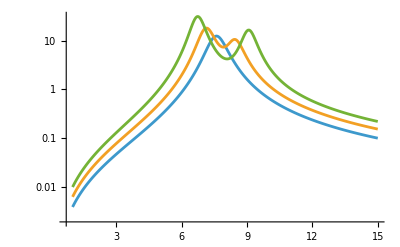

```mathematica
ListLinePlot[{qextAlSCDrudeList[[1]],qextAlSCDrudeList[[2]],qextAlSCDrudeList[[3]]},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
ResRojoAlDrude=GoldenSearchMax[qextAlSCDrudePlot[[#]],4,9] &/@Range[1,17]
ResAzulAlDrude=GoldenSearchMax[qextAlSCDrudePlot[[#]],7.6,15] &/@Range[1,17]
```

{7.60161,7.14167,6.74203,6.40113,6.10714,5.85,5.62185,5.41764,5.2359,5.06803,4.91643,4.7792,4.65,4.5343,4.42336,4.32108,4.2267}

{7.60161,8.43393,9.08045,9.55955,9.93899,10.2453,10.4983,10.708,10.892,11.0488,11.1841,11.3007,11.4072,11.5015,11.5911,11.6644,11.7375}

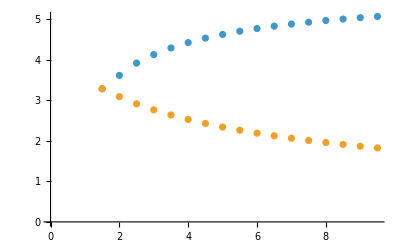

```mathematica
ListPlot[{Transpose[{barrido,ResAzulAuDrude}],Transpose[{barrido,ResRojoAuDrude}]}]
```

```mathematica
ListLinePlot[{qextAuSCDrudePlot[[1]]},PlotRange->All]
```

-Graphics-

```mathematica
adios1=ListPlot[Table[{ResRojoAuDrude[[x]],qextAuSCDrudePlot[[x]][ResRojoAuDrude[[x]]]},{x,1,16}],ScalingFunctions->"Log"];
adios2=ListPlot[Table[{ResAzulAuDrude[[x]],qextAuSCDrudePlot[[x]][ResRojoAuDrude[[x]]]},{x,1,16}],ScalingFunctions->"Log"];
```

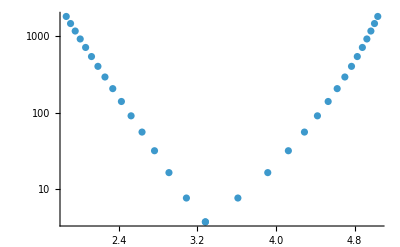

```mathematica
Show[adios1,adios2,PlotRange->All]
```

```mathematica
qextAlSCOCList=Table[{w,CextSC[#,#,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[3]]},{w,1,16,0.05}]&/@barrido;
qextAlSCOCBarrido=Table[CextSC[#,#,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[3]],{w,1,16,0.05}]&/@barrido;
qextAlSCOCPlot=Interpolation[Transpose[{omegasAl,qextAlSCOCBarrido[[#]]}]]&/@Range[1,17];
```

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1474.97-314.994 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1474.97-314.994 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

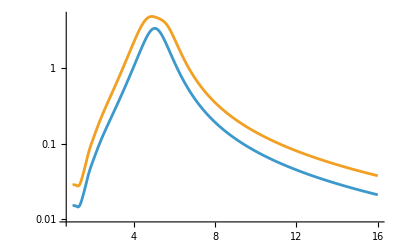

```mathematica
ListLinePlot[{qextAlSCOCList[[1]],qextAlSCOCList[[2]]},PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
ResRojoAlOC=GoldenSearchMax[qextAlSCOCPlot[[#]],2.5,6.2] &/@Range[1,17]
ResAzulAlOC=GoldenSearchMax[qextAlSCOCPlot[[#]],5.43,16] &/@Range[2,17]
```

{5.0415,4.89714,4.56005,4.32541,4.13178,3.96551,3.82112,3.69468,3.5827,3.483,3.39351,3.31213,3.23837,3.17026,3.10738,3.0494,2.99493}

{5.43,5.78213,6.1187,6.35,6.53056,6.67699,6.79958,6.9026,6.99274,7.07018,7.13905,7.19991,7.25332,7.30204,7.3469,7.38676}

```mathematica
hola=Table[{w,CextSC[4,4,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[3]]},{w,1,11,0.05}];
hola2=Table[CextSC[4,4,1.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[3]],{w,1,11,0.05}];
```

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1474.97-314.994 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1474.97-314.994 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
barrido
```

{1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5}

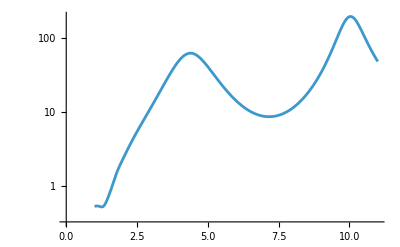

```mathematica
ListLinePlot[hola,ScalingFunctions->"Log"]
```

```mathematica
omegasAl0=Range[1,11,0.05];
```

```mathematica
qextAlSCOCPlot0=Interpolation[Transpose[{omegasAl0,hola2}]];
```

```mathematica
qextAlSCOCPlot0
```

InterpolatingFunction[…]

```mathematica
GoldenSearchMax[qextAlSCOCPlot0,9,11]
```

10.0389

```mathematica
polAlSCTotListAbs1=Table[{w,Abs[polarizabilitySC[7.5,7.5,7.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[1]]]/(4*Pi*7.5*7.5*7.5/3)},{w,1,16,0.01}];
polAlSCDrudeListAbs1=Table[{w,Abs[polarizabilitySC[7.5,7.5,7.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[3]]]/(4*Pi*7.5*7.5*7.5/3)},{w,1,16,0.01}];
polAlSCOCListAbs1=Table[{w,Abs[polarizabilitySC[7.5,7.5,7.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[5]]]/(4*Pi*7.5*7.5*7.5/3)},{w,1,16,0.01}];
polAlSCTotListArg1=Table[{w,Arg[polarizabilitySC[7.5,7.5,7.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[1]]]},{w,1,16,0.01}];
polAlSCDrudeListArg1=Table[{w,Arg[polarizabilitySC[7.5,7.5,7.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[3]]]},{w,1,16,0.01}];
polAlSCOCListArg1=Table[{w,Arg[polarizabilitySC[7.5,7.5,7.5,1,w,wpAl,gAl,fAl,w0Al,sigmaAl,mu,hvFAl][[5]]]},{w,1,16,0.01}];
```

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1425.06-308.558 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1434.96-309.852 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.9-311.143 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

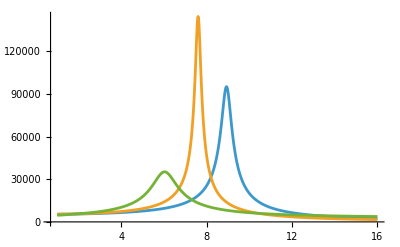

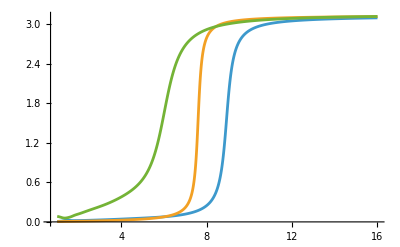

```mathematica
ListLinePlot[{polAlSCTotListAbs1,polAlSCDrudeListAbs1,polAlSCOCListAbs1},PlotRange->All]
ListLinePlot[{polAlSCTotListArg1,polAlSCDrudeListArg1,polAlSCOCListArg1},PlotRange->All]
```